```mathematica
singpert[x_,c_, beta_, n_, d_]:= x^n+c+beta/(x^d)
```

```mathematica
singpert[1,1,1,1,1]
```

3

```mathematica
singpert2[x_,c_,beta_]:=singpert[x,c,beta,2,2]
```

```mathematica
f1[x_,c_,beta_]:=singpert2[x,c,beta];
f2[x_,c_,beta_]:= f1[f1[x,c,beta],c, beta]
f3[x_,c_,beta_]:=f2[f1[x,c,beta],c,beta]
f4[x_,c_,beta_]:=f3[f1[x,c,beta],c,beta]
```

```mathematica
Manipulate[Plot[{CRIT,x, (*f2[x,c,.001],f1[x,c,.001],*)f2[x,c,.001]},{x,-10*zoom,10*zoom},Epilog->{Line[{{CRIT,-10},{CRIT, 10}}]},PlotRange->zoom*10,ImagePadding->{{25,10},{10,10}}, ImageSize->1300],{{c,-.14,"param"},-1.3,1.3,.001,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},{{zoom,.15,"zoom"},.1,4,.1,ImageSize->Small,ControlPlacement->Left},SaveDefinitions->True,TrackedSymbols->Manipulate]
```

```mathematica
Manipulate[Plot[{f2[x,c,.001]-x(*,f2[x,c,.001]-x,f3[x,c,.001]-x*)},{x,-2*zoom,2*zoom},PlotLegends->"Expressions"],{{c,1},-2,1,.01},{{zoom,1},.1,1}]
```

```mathematica
sols=Solve[f2[x,c,.001]==x,x,Reals];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

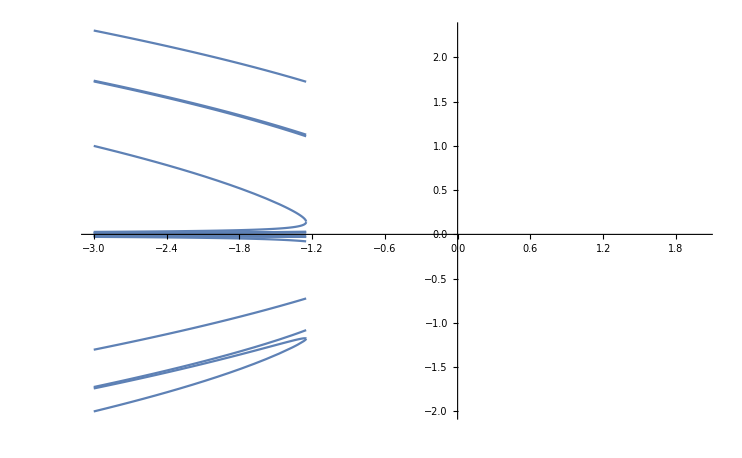

```mathematica
Plot[x/.sols,{c,-3,2}]
```

```mathematica
Manipulate[
Fp=x/.(mysols/.cval->c);
If[!NumericQ[Fp]||Im[Fp]≠0,Fp=0];
p=Plot[{x,f3[x,c,.001],.001^(.25),-.001^(.25) },{x,-10*zoom,10*zoom},
Epilog->{Arrowheads[.01],Arrow[ itinerary[(f3[#,c,.001])&,.001^(.25),n+1]],Arrow[ itinerary[(f3[#,c,.001])&,Fp-.00001,n2+1]], 
	Red,Dashed, Line[{{{.001^(.25),-10},{.001^(.25),10}},
	{{-.001^(.25),-10},{-.001^(.25),10}},
	{{Fp,-10},{Fp,10}},
	{{-10,Fp},{10,Fp}}
}]},PlotRange->zoom*10,ImagePadding->{{25,10},{10,10}}, ImageSize->1300];
Button["Export",Export["~/Thesis/plot"<>ToString[c]<>".pdf",p]]Show[p]
,{{c,-.092495,"param"},-1.3,1.3,stepsize,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{n,1,"iterates"},1,100,1,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{n2,0,"iterates2"},1,100,1,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{x0,1.0845,"seed"},-2,2,stepsize,ImageSize->Small,Appearance->"Labeled",ControlPlacement->Left},
{{zoom,.112,"zoom"},.01,.5,.001,ImageSize->Small,ControlPlacement->Left}, {{stepsize,.001,"Step Size"},0,1,.0001,ImageSize->Small,ControlPlacement->Left},SaveDefinitions->True,TrackedSymbols->Manipulate]
```